The following code is part of Natasha Dada’s Wolfram Summer School 2018 project, An Analysis of Word Choice in the Real Estate Industry. This code identifies the most frequently used words and their success in a collection of MLS house listings from the Boston area from April-June 2018.

A list of house listings, each in the form {house description (string), percent difference between listing and selling price of the house (number)}:

```mathematica
data = Get["data.mx"];
```

The house descriptions stemmed without stopwords or numerical values:

```mathematica
tokenizedData = Transpose[{Select[WordStem@TextWords@ToLowerCase@DeleteStopwords@First[#],!StringContainsQ[#,{"0","1","2","3","4","5","6","7","8","9"}]&]&/@data,data[[All,2]]}];
```

A neural net from the Wolfram Neural Net Repository for feature extraction of words:

```mathematica
glove=
NetModel["GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data"];
```

A list of words from every listing in the form {word, score of listing}:

```mathematica
allWords = Flatten[Transpose[{First[#],Table[Last[#],Length[First[#]]]}]&/@tokenizedData,1];
```

A list of words that occur in more than 1% of listings, scored according to the average success of the listings in which a word was used:

```mathematica
mostFrequentWords = Select[GatherBy[allWords,First],Length[#]>30&]; mostFrequentWords=SortBy[{First[First[#]],Mean[Last/@#]}&/@mostFrequentWords,Last];
```

A list of frequent words whose listing has a negative score:

```mathematica
negativeWords=Select[mostFrequentWords,Last[#]<0&];
```

Negative scores rescaled between 0 and 0.5 which will correspond to different shades of red:

```mathematica
rescaledNegativeScores = Rescale[negativeWords[[All,2]],MinMax[negativeWords[[All,2]]],{0,0.5}];
```

A list of frequent words whose listing has a positive score:

```mathematica
positiveWords=Select[mostFrequentWords,Last[#]>0&];
```

Positive scores rescaled between 0.5 and 1 which will correspond to different shades of green:

```mathematica
rescaledPositiveScores = Rescale[positiveWords[[All,2]],MinMax[positiveWords[[All,2]]],{0.5,1}];
```

The scores of all the most frequent words rescaled to values between 0 and 1:

```mathematica
rescaledScores = Join[rescaledNegativeScores,rescaledPositiveScores];
```

A list of each top word in the form {word, rescaled score}:

```mathematica
rescaledWords = Transpose[{mostFrequentWords[[All,1]],rescaledScores}];
```

A feature space plot that used a neural net to map each word. The color of each word corresponds to its success:

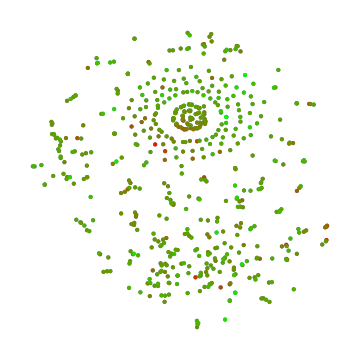

```mathematica
FeatureSpacePlot[Style[First[#],RGBColor[1-Last[#],Last[#],0]]&/@rescaledWords,FeatureExtractor->glove,LabelingFunction->Tooltip,ImageSize->Medium,PlotStyle->Directive[PointSize[Medium]]]
```

The words that were unsuccessful in order from most unsuccessful to least unsuccessful (worst to best):

```mathematica
mostNegativeWords = First/@Select[mostFrequentWords,Last[#]< -1&]
```

{wharf,zone,valet,harbor,servic,residenti,hour,total,leas,interior,concierg,loung,beacon,sf,west}

The words that were successful in order from least successful to most successful (worst to best):

```mathematica
mostPositiveWords=First/@Select[mostFrequentWords,Last[#]> 1&]
```

{access,spot,height,room,master,work,enclos,heater,third,ga,w,manag,add,entir,awai,enter,overlook,island,share,point,effici,finish,avail,consist,util,parlor,common,level,heat,histor,fulli,incred,design,ton,fireplac,av,fill,make,plu,doubl,commut,fixtur,cook,car,beach,rare,courtyard,surround,prime,walk,backyard,pantri,area,shaker,crown,transport,deed,situat,impecc,local,commun,complet,block,outdoor,score,school,live,duplex,squar,logan,covet,side,top,bedroom,soar,stop,larg,hill,complex,come,window,overs,south,boston',energi,highlight,want,us,featur,breathtak,patio,field,enjoi,bed,longwood,ceil,orang,enorm,brand,street,amen,maverick,investor,entertain,lobbi,counter,kitchen,cabinet,outsid,space,glass,station,villag,floor,minut,thermostat,steel,vaniti,roof,great,beautifulli,dine,comfort,person,plan,insul,d,charact,layout,maintain,readi,desir,excel,natur,hardwood,built-in,bosch,dryer,extra,renov,washer,air,privat,upstair,todai,bike,gener,applianc,breakfast,spaciou,brick,stair,eat,condominium,mbta,easi,pristin,end,contemporari,ss,king,throughout,closet,beauti,close,s,flow,gleam,townhous,bonu,call,dai,subwai,line,locat,hvac,feel,short,french,skylight,pet,sink,buyer,countertop,c,granit,appoint,nice,burn,sought,w/,second,tall,st,option,fee,bai,wood,just,gorgeou,size,fridg,food,entranc,conveni,offer,open,recent,addit,drivewai,restaur,huge,marbl,cabinetri,chanc,mold,time,door,vibrant,laundri,detail,perfectli,friendli,offic,deck,occupi,paint,central,condo,stainless,small,storag,boast,coffe,ideal,dorchest,newburi,market,cancel,chic,sleek,perfect,amaz,neighborhood,hot,invit,exclus,quiet,ampl,hous,high-end,east,updat,red,look,heart,skylin,beam,bright,chef',ac,ashmont,sun,near,upper,hottest,charlestown,yard,shop,airport,light,provid,reserv,attach,modern,landscap,tile,associ,t,studio,expos,seat,highli,accent,porch,train,upgrad,distanc,basement,show,low,exposur,wait,love,bremen,spring,sunni,abund,purchas,life,classic,stain,pleas,plenti,gem,miss,wide,mapl,/c,,main,origin,front,sun-fil,welcom,white,urban,sale,wonder,best,summer,green,right,multipl,stove,warm,possibl,seller,fenc,in-unit,dishwash,sundai,lead,move,cafe,cambridg,backsplash,recess,savin,tree-lin,rear,charm,nestl,fantast,truli,off-street,fabul,siena,due,saturdai,stylish,valu,fenwai,pm,oasi,monument,fan,nurseri,mantel,mondai,april,relax,tree,review,march,list,slide,tuesdai,directli,coplei}